```mathematica
β = 0.07; Ω = 0.4;
```

```mathematica
(*Definición del sistema EDO explícito para mayor velocidad y estabilidad*)ecuacionesOptimizadas={x'[t]==I*((Ω/2)*x[t]-(β^2/2)*t)*x[t]*2-(I*Ω/2)*(1+x[t]^2),y'[t]==(I/2)*(Ω*x[t]-(β^2)*t),z'[t]==-(I*Ω/2)*Exp[2*y[t]],x[-160]==0,y[-160]==0,z[-160]==0};
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[ecuacionesOptimizadas,{x,y, z},{t,-180, 180},AccuracyGoal->10, PrecisionGoal->10];
```

```mathematica
{x'[t]-  2y'[t] x[t] + (I Ω)/2(1 + x[t]^2)== 0 ,y'[t] == I/2(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ (I Ω)/2 == 0, x[-160]==y[-160]==z[-160]== 0}
```

```mathematica
I1[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20, Method->"LevinRule"]]^2
```

```mathematica
I2[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20, Method->"LevinRule"]]^2
```

```mathematica
S[Γ_?NumericQ,ω_?NumericQ,T_?NumericQ, T0_?NumericQ]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
step = 0.03;Γ = 0.1;T0=-178;
```

```mathematica
DTrace01=ParallelTable[{ν,S[Γ,ν,-50,T0]},{ν,-1.4,1.4,step}];
DTrace02= ParallelTable[{ν,S[Γ,ν,-40,T0]},{ν,-1.4,1.4,step}];
DTrace03=ParallelTable[{ν,S[Γ,ν,-30,T0]},{ν,-1.4,1.4,step}];
DTrace04=  ParallelTable[{ν,S[Γ,ν,-25,T0]},{ν,-1.4,1.4,step}];
DTrace05=ParallelTable[{ν,S[Γ,ν,-20,T0]},{ν,-1.4,1.4,step}];
DTrace06=ParallelTable[{ν,S[Γ,ν,-15,T0]},{ν,-1.4,1.4,step}];
DTrace07= ParallelTable[{ν,S[Γ,ν,-10,T0]},{ν,-1.4,1.4,step}];
DTrace08=  ParallelTable[{ν,S[Γ,ν,-5,T0]},{ν,-1.4,1.4,step}];
DTrace09=  ParallelTable[{ν,S[Γ,ν,0,T0]},{ν,-1.4,1.4,step}];
```

```mathematica
DTrace10=ParallelTable[{ν,S[Γ,ν,0,T0]},{ν,-1.0,1.8,step}];
DTrace11=ParallelTable[{ν,S[Γ,ν,5,T0]},{ν,-1.0,1.8,step}];
DTrace12=ParallelTable[{ν,S[Γ,ν,10,T0]},{ν,-1.0,1.8,step}];
DTrace13=ParallelTable[{ν,S[Γ,ν,15,T0]},{ν,-1.0,1.8,step}];
DTrace14=ParallelTable[{ν,S[Γ,ν,20,T0]},{ν,-1.0,1.8,step}];
DTrace15=ParallelTable[{ν,S[Γ,ν,40,T0]},{ν,-1.0,1.8,step}];
DTrace16=ParallelTable[{ν,S[Γ,ν,60,T0]},{ν,-1.0,1.8,step}];
DTrace17=ParallelTable[{ν,S[Γ,ν,80,T0]},{ν,-1.0,1.8,step}];
DTrace18=ParallelTable[{ν,S[Γ,ν,100,T0]},{ν,-1.0,1.8,step}];
```

```mathematica
Trace01=Table[Insert[DTrace01[[j]],1,2],{j,1,Length[DTrace01]}];
Trace02=Table[Insert[DTrace02[[j]],2,2],{j,1,Length[DTrace02]}];
Trace03=Table[Insert[DTrace03[[j]],3,2],{j,1,Length[DTrace03]}];
Trace04=Table[Insert[DTrace04[[j]],4,2],{j,1,Length[DTrace04]}];
Trace05=Table[Insert[DTrace05[[j]],5,2],{j,1,Length[DTrace05]}];
Trace06=Table[Insert[DTrace06[[j]],6,2],{j,1,Length[DTrace06]}];
Trace07=Table[Insert[DTrace07[[j]],7,2],{j,1,Length[DTrace07]}];
Trace08=Table[Insert[DTrace08[[j]],8,2],{j,1,Length[DTrace08]}];
Trace09=Table[Insert[DTrace09[[j]],9,2],{j,1,Length[DTrace09]}];
```

```mathematica
Trace10=Table[Insert[DTrace10[[j]],10,2],{j,1,Length[DTrace10]}];
Trace11=Table[Insert[DTrace11[[j]],11,2],{j,1,Length[DTrace11]}];
Trace12=Table[Insert[DTrace12[[j]],12,2],{j,1,Length[DTrace12]}];
Trace13=Table[Insert[DTrace13[[j]],13,2],{j,1,Length[DTrace13]}];
Trace14=Table[Insert[DTrace14[[j]],14,2],{j,1,Length[DTrace14]}];
Trace15=Table[Insert[DTrace15[[j]],15,2],{j,1,Length[DTrace15]}];
Trace16=Table[Insert[DTrace16[[j]],16,2],{j,1,Length[DTrace16]}];
Trace17=Table[Insert[DTrace17[[j]],17,2],{j,1,Length[DTrace17]}];
Trace18=Table[Insert[DTrace18[[j]],18,2],{j,1,Length[DTrace18]}];
```

```mathematica
grafico3d =Show[Graphics3D[{
Red,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace01],
Black,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace02],
RGBColor[0,0.8,0.8],Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace03],
Purple,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace04],
RGBColor[0,0.7,0.4],Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace05],
Orange,Thickness[0.0025],BSplineCurve[Trace06],
Purple,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace07],
Black,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace09],
Blue,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace08],
Red,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace10],
Green,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace11]
}],
Axes->{True,True,True},PlotRange->All,
Ticks->{Automatic,{{1,-100},{2,-50},{3,-36},{4,-24}{5,-8},{6,0},{7,8},{8,24}, {9, 36}, {10,80}, {11,120}},None},
TicksStyle->Directive[12,Black],BoxRatios->{3,5.5,2},
Boxed->False,AxesEdge->{{0,0},{1,0},{1,1}},ImageSize->700, AxesLabel->{
Style["ω_0",20,Black,FontFamily->"Times New Roman"],
Style["t",20,Black,FontFamily->"Times New Roman"]}];
grafico3d
```

-Graphics3D-

```mathematica
(*Definimos una paleta de 11 colores basada en un degradado*)
paletaTiempo=Table[Blend[{RGBColor[0.1,0.2,0.6],RGBColor[0.5,0.1,0.5],RGBColor[0.8,0.2,0.2]},i/10],{i,0,18}];

(*trazas en orden cronológico*)
trazasCodigo={Trace01,Trace02,Trace03,Trace04,Trace05,Trace06,Trace07,Trace08,Trace09,Trace10,Trace11,Trace12,Trace13,Trace14,Trace15,Trace16,Trace17,Trace18};

graficoPublicacion3D=Show[Graphics3D[Table[{paletaTiempo[[i]],AbsoluteThickness[1.5],BSplineCurve[trazasCodigo[[i]]]},{i,1,Length[trazasCodigo]}]],Axes->True,PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1,1.5,0.6},Boxed->False,Ticks->{Automatic,{{1,"-100"},{2,"-50"},{3,"-36"},{4,"-24"},{5,"-8"},{6,"0"},{7,"8"},{8,"24"},{9,"36"},{10,"80"},{11,"120"}},Automatic},BaseStyle->{FontFamily->"Times New Roman",FontSize->10,Black},TicksStyle->Directive[FontSize->9,Black],AxesLabel->{Style["ω",FontSize->12,Italic],Style["t",FontSize->12,Italic],Style["S(ω, t)",FontSize->12]},ImageSize->600 ]
```

-Graphics3D-

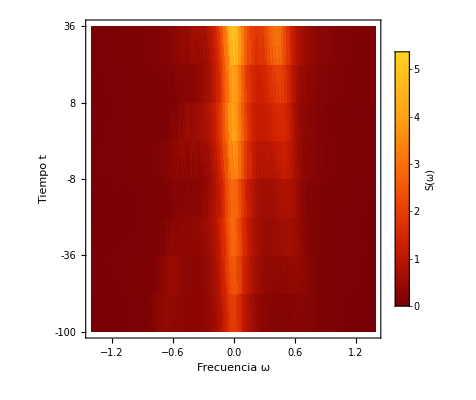

```mathematica
(*Combinamos los datos en una matriz {ω,t,S}*)
datosUnificados=Join[Trace01,Trace02,Trace03,Trace04,Trace05,Trace06,Trace07,Trace08,Trace09];

graficoDensidad=ListDensityPlot[datosUnificados,PlotRange->All,ColorFunction->"SolarColors",InterpolationOrder->3,Frame->True,FrameTicks->{Automatic,{{1,"-100"},{2,"-50"},{3,"-36"},{4,"-24"},{5,"-8"},{6,"0"},{7,"8"},{8,"24"},{9,"36"},{10,"80"},{11,"120"}}},BaseStyle->{FontFamily->"Times New Roman",FontSize->10,Black},FrameLabel->{Style["Frecuencia ω",Italic],Style["Tiempo t",Italic]},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["S(ω)",FontSize->10],LabelStyle->{FontSize->9}],After],ImageSize->400]
```

```mathematica
ListPlot3D[datosCompletos,Mesh->{20,10},
(*Malla para guiar el ojo en ambas direcciones*)
MeshStyle->Opacity[0.3],ColorFunction->"Rainbow",AxesLabel->{Style["ω",16,Italic],Style["t",16,Italic],Style["S",16,Italic]},LabelStyle->Directive[Black,FontFamily->"Times New Roman"],Boxed->False,PlotRange->All,ViewPoint->{2,-2,1}, ImageSize->Large ]
```

-Graphics3D-

```mathematica
(*Agrupamos solo los perfiles 2D generados por ParallelTable*)perfilesTemporales={DTrace01,DTrace02,DTrace03,DTrace04,DTrace05,DTrace06,DTrace07,DTrace08,DTrace09,DTrace10,DTrace11, DTrace12, DTrace13, DTrace14, DTrace15, DTrace16, DTrace17, DTrace18};

(*Etiquetas de tiempo correspondientes a tus trazas*)
tiempos={-50,-40,-30,-25,-20,-15,-10,-5,0,0,5,10,15,20,40,60,80,100};

ListAnimate[Table[ListLinePlot[perfilesTemporales[[i]],PlotRange->{All,{0,Max[datosCompletos[[All,3]]]}},(*Mantiene el eje Y estático basado en el máximo global*)PlotStyle->Directive[Thick,Darker[Blue]],Frame->True,FrameLabel->{Style["ω",16],Style["S",16]},PlotLabel->Style[Row[{"Tiempo t = ",tiempos[[i]]}],16],ImageSize->Large],{i,1,Length[perfilesTemporales]}],AnimationRate->2]
```

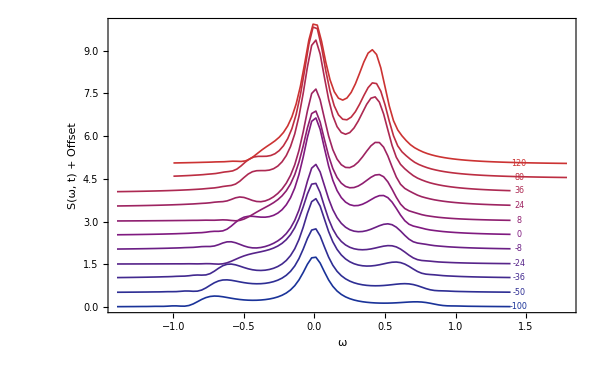

```mathematica
(*Extraemos los datos {ω,S} de las tablas originales DTrace*)
listas2D={DTrace01,DTrace02,DTrace03,DTrace04,DTrace05,DTrace06,DTrace07,DTrace08,DTrace09,DTrace10,DTrace11};
tiempos={-100,-50,-36,-24,-8,0,8,24,36,80,120};

(*Añadimos un offset vertical para separar las líneas artificialmente*)
offset=0.5; 
datosConOffset=Table[Table[{punto[[1]],punto[[2]]+(i-1)*offset},{punto,listas2D[[i]]}],{i,1,Length[listas2D]}];

graficoLineasApiladas=ListLinePlot[datosConOffset,PlotStyle->Table[Directive[paletaTiempo[[i]],AbsoluteThickness[1.2]],{i,1,11}],PlotRange->All,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->10,Black},FrameLabel->{Style["ω",Italic],Style["S(ω, t) + Offset",Italic]},(*Colocamos etiquetas de texto al lado derecho de cada curva para indicar el tiempo*)Epilog->Table[Text[Style[ToString[tiempos[[i]]],FontSize->8,paletaTiempo[[i]]],{1.45,listas2D[[i]][[-1,2]]+(i-1)*offset},{-1,0}],{i,1,Length[tiempos]}],ImageSize->600]
```

```mathematica
(*Definimos una paleta de 11 colores basada en un degradado*)
paletaTiempo=Table[Blend[{RGBColor[0.1,0.2,0.6],RGBColor[0.5,0.1,0.5],RGBColor[0.8,0.2,0.2]},i/10],{i,0,18}];
paletaTiempo=Table[Blend[{RGBColor[0.1,0.2,0.6],RGBColor[0.5,0.1,0.5],RGBColor[0.8,0.2,0.2]},i/10],{i,0,10}];
paletaMagma=Table[Blend[{Black,Purple,RGBColor[0.8,0.2,0.2],Orange},i/10],{i,0,10}];
paletaOceano=Table[Blend[{RGBColor[0.1,0.1,0.4],RGBColor[0.2,0.6,0.6],RGBColor[0.9,0.8,0.2]},i/10],{i,0,10}];
paletaSunset=Table[ColorData["SunsetColors"][i/10],{i,0,10}];
paletaMonocromatica=Table[Blend[{RGBColor[0.05,0.1,0.25],RGBColor[0.6,0.7,0.85]},i/10],{i,0,10}];

trazasCodigo={Trace01,Trace02,Trace03,Trace04,Trace05,Trace06,Trace07,Trace08,Trace09};
trazasCodigo2={Trace10,Trace11,Trace12,Trace13,Trace14,Trace15,Trace16,Trace17,Trace18};

(*Altura de la base para el sombreado*)
zBase=0;
```

```mathematica
grafico3DSombreado= Style[Show[Graphics3D[Table[Module[{puntos,ptInicial,ptFinal,puntosPoligono},
(*Extraemos los puntos de la traza actual*)
puntos=trazasCodigo2[[i]];
(*Identificamos los extremos para proyectarlos al suelo*)
ptInicial=puntos[[1]];
ptFinal=puntos[[-1]];
(*Cerramos la curva creando una lista de puntos para el polígono*)
(*Añadimos el punto final proyectado a z=0 y el punto inicial proyectado a z=0*)
puntosPoligono=Join[puntos,{{ptFinal[[1]],ptFinal[[2]],zBase},{ptInicial[[1]],ptInicial[[2]],zBase}}];
{
(*1. EL ÁREA SOMBREADA*)(*Quitamos el borde del polígono para evitar líneas verticales feas en los extremos*)
EdgeForm[None],
(*Usamos el color de la paleta con cierta opacidad para poder ver a través ligeramente*)
FaceForm[Directive[paletaSunset[[i]],Opacity[0.3]]],Polygon[puntosPoligono],
(*2. LA CURVA SUPERIOR (TRAZA)*)(*Dibujamos la línea superior un poco más oscura para que resalte sobre su propio sombreado*)
Darker[paletaSunset[[i]],0.6],AbsoluteThickness[1.5],
(*Usamos Line en lugar de BSplineCurve para que coincida perfectamente con el borde del polígono*)
Line[puntos]}],{i,1,Length[trazasCodigo2]}]],
(*---CONFIGURACIÓN DE EJES Y ESTÉTICA---*)
(*---ViewPoint->{0.8,-2.2,1.2},ViewVertical->{0.0,0.0,1.0},ViewCenter->{0.5,0.5,0.5},ViewVector->Automatic,---*)
Axes->True,PlotRange->{-0.2,15.2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1,1.5,0.6},Boxed->False,Ticks->{Automatic,{{1,"-100"},{2,"-80"},{3,"-60"},{4,"-40"},{5,"-32"},{6,"-24"},{7,"-16"},{8,"-8"},{9,"0"}},Automatic},
(*---Ticks->{Automatic,{{10,"0"},{11,"8"},{12,"16"},{13,"24"},{14,"32"},{15,"40"},{16,"60"},{17,"80"},{18,"100"}},Automatic},---*)
BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},TicksStyle->Directive[FontSize->12,Black],Lighting->"Neutral",
AxesLabel->{Style["ω",FontSize->16,Italic],Style["t",FontSize->16,Italic],Style["",FontSize->16]},ImageSize->700 ], Antialiasing->True]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
perspectivaPublicacion={ViewPoint->{2.2,-2.8,1.4},ViewVertical->{0.0,0.0,1.0},ViewCenter->{0.5,0.5,0.5},ViewVector->Automatic};
```

```mathematica
graficoFinalFijado=Show[grafico3DSombreado,perspectivaPublicacion];
```

```mathematica
Export["./Documents/Maestria/Work/articulo LZ/escalera/deseño4.tiff",grafico3DSombreado,"AllowRasterization"->False, ImageResolution->800]
```

./Documents/Maestria/Work/articulo LZ/escalera/deseño4.tiff

```mathematica
grafico3DSombreado= Style[Show[Graphics3D[Table[Module[{puntos,ptInicial,ptFinal,puntosPoligono},
(*Extraemos los puntos de la traza actual*)
puntos=trazasCodigo2[[i]];
(*Identificamos los extremos para proyectarlos al suelo*)
ptInicial=puntos[[1]];
ptFinal=puntos[[-1]];
(*Cerramos la curva creando una lista de puntos para el polígono*)
(*Añadimos el punto final proyectado a z=0 y el punto inicial proyectado a z=0*)
puntosPoligono=Join[puntos,{{ptFinal[[1]],ptFinal[[2]],zBase},{ptInicial[[1]],ptInicial[[2]],zBase}}];
{
(*1. EL ÁREA SOMBREADA*)(*Quitamos el borde del polígono para evitar líneas verticales feas en los extremos*)
EdgeForm[None],
(*Usamos el color de la paleta con cierta opacidad para poder ver a través ligeramente*)
FaceForm[Directive[paletaSunset[[i]],Opacity[0.3]]],Polygon[puntosPoligono],
(*2. LA CURVA SUPERIOR (TRAZA)*)(*Dibujamos la línea superior un poco más oscura para que resalte sobre su propio sombreado*)
Darker[paletaSunset[[i]],0.6],AbsoluteThickness[1.5],
(*Usamos Line en lugar de BSplineCurve para que coincida perfectamente con el borde del polígono*)
Line[puntos]}],{i,1,Length[trazasCodigo2]}]],
(*---CONFIGURACIÓN DE EJES Y ESTÉTICA---*)
(*---ViewPoint->{0.8,-2.2,1.2},ViewVertical->{0.0,0.0,1.0},ViewCenter->{0.5,0.5,0.5},ViewVector->Automatic,---*)
Axes->True,PlotRange->{-0.2,15.2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},BoxRatios->{1,1.5,0.6},Boxed->False,
Ticks->{Automatic,{{10,"0"},{11,"8"},{12,"16"},{13,"24"},{14,"32"},{15,"40"},{16,"60"},{17,"80"},{18,"100"}},Automatic},
BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},TicksStyle->Directive[FontSize->12,Black],Lighting->"Neutral",
AxesLabel->{Style["ω",FontSize->16,Italic],Style["t",FontSize->16,Italic],Style["",FontSize->16]},ImageSize->700 ], Antialiasing->True]
```

-Graphics3D-

-Graphics3D-